# NG^21 P_11. Архитектура свёрточных нейронных сетей

Бельской Екатерины,
 2 курс 5 группа

## 1. Извлечение признаков

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Fold[Partition[#,#2]&,BinaryReadList[F,"Byte",ByteOrdering->+1],{Cols,Rows}]/255.;
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]]
```

{{60000},{60000,28,28}}

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]]
```

{{10000},{10000,28,28}}

```mathematica
DynamicModule[{m=3},Grid[{
{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{
Manipulate[Style[Train⟦1,n⟧,Bold,24+2m]->Image[1-Train⟦2,n⟧,ColorSpace->"GrayScale",Magnification->m],{{n,37267,"Train"},1,Length@Train⟦1⟧,1,Appearance->"Labeled"},Paneled->False,ControlPlacement->Top],
Manipulate[Style[Test⟦1,n⟧,Bold,24+2m]->Image[1-Test⟦2,n⟧,ColorSpace->"GrayScale",Magnification->m],{{n,4655,"Test"},1,Length@Test⟦1⟧,1,Appearance->"Labeled"},Paneled->False,ControlPlacement->Top]}},Frame->All,FrameStyle->Gray]]
```

Списки номеров растров соответствующих цифр

6 : 14, 19, 33, 37
8 : 18, 32, 42, 47
9 : 5, 20, 23, 34

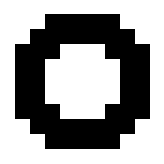

```mathematica
ArrayPlot[ker1=DiskMatrix[4, 9]-DiskMatrix[2,9]]
```

```mathematica
l6={14, 19, 33,37};
l8={18, 32, 42,47};
l9={5, 20, 23,34};
```

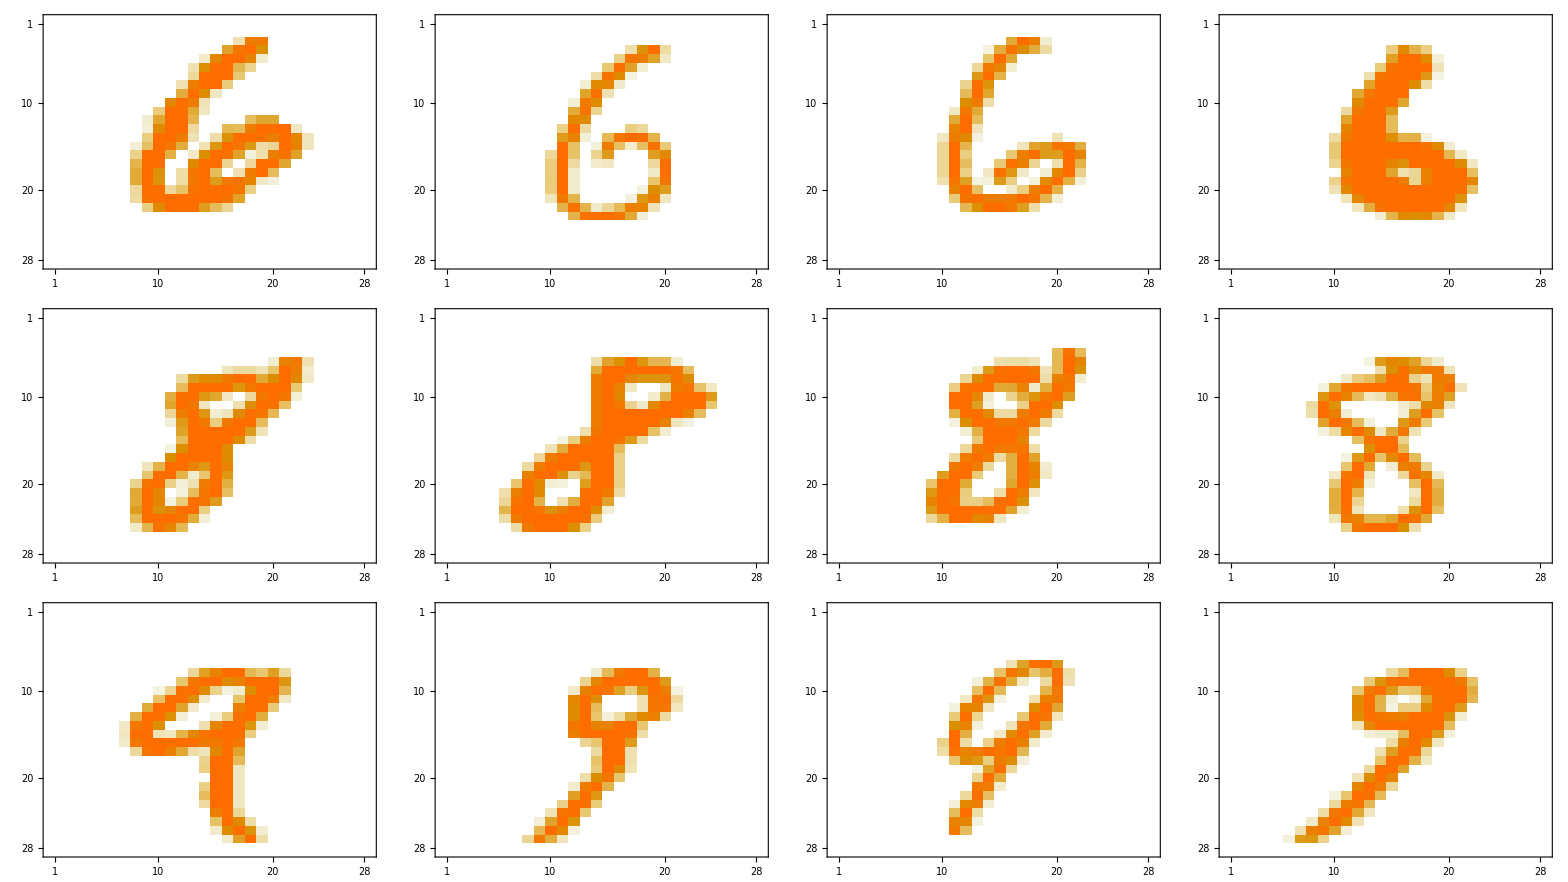

```mathematica
Grid[{MatrixPlot@Train⟦2,#⟧&/@l6,MatrixPlot@Train⟦2,#⟧&/@l8,
MatrixPlot@Train⟦2,#⟧&/@l9}]
```

Функция отображения вычисленной свертки с выбранными растрами, при элементах в маске 1 и -1

```mathematica
sv:=MatrixPlot[ListConvolve[ker1/.{0->-1}, Train⟦2,#⟧], ColorFunction->"GreenPinkTones"]&/@#&
```

```mathematica
Grid[{sv[l6],sv[l8],sv[l9]}]
```

Функция отображения вычисленной свертки с выбранными растрами, при элементах в маске 1 и 0

```mathematica
sv1:=MatrixPlot[ListConvolve[ker1, Train⟦2,#⟧], ColorFunction->"GreenPinkTones"]&/@#&
```

```mathematica
Grid[{sv1[l6],sv1[l8],sv1[l9]}]
```

Из картинок видно, что граница хорошо прорисовывается в первом случае, когда элементы маски не 0. Если есть нули, то значение пикселя будем просто зануляться и тем самым при свертке не будет учитываться. При - 1 значения сохраняются, и виден контраст между "внутренностью" рисунка и его границей. Поэтому лучше пользоваться маской с ненулевыми значениями.

## 2. Свёрточный слой

### 2.1 Подслой свёртки

```mathematica
kmWeight1=Map[{First@#,Partition[Rest@#,5]}&,RandomReal[{-.1,.1},{6 ,26}]];
```

```mathematica
Grid[{MatrixPlot[#⟦2⟧,ColorFunction->"GreenPinkTones",Frame->False,PlotLabel->ToString[#⟦1⟧]]&/@kmWeight1},Frame->All]
```

```mathematica
rastr=Train⟦2,3⟧;
```

```mathematica
Dimensions[rastr]
```

{28,28}

```mathematica
kmWeight1⟦3⟧;
First@% + ListConvolve[Last@%,rastr];
Ramp@%;
Partition[%, {2,2}];
%//Dimensions
Map[Max,%%,{2}];
%//Dimensions
```

{12,12,2,2}

{12,12}

Подслой свертки

```mathematica
ClearAll[kmConvolutionLayer1];kmConvolutionLayer1=Function[X, First@# + ListConvolve[Last@#,X]&/@kmWeight1]
```

Function[X,(First[#1]+ListConvolve[Last[#1],X]&)/@kmWeight1]

```mathematica
kmConvolutionLayer1@rastr//Dimensions
```

{6,24,24}

Все шаги поэтапно с изображениями

```mathematica
kmConvolutionLayer1@rastr;
Dimensions@%
MatrixPlot[#,Mesh->True, ColorFunction->"GreenPinkTones", ImageSize->100]&/@%%
Ramp@%%%;
MatrixPlot[#,Mesh->True,ColorFunction->"GreenPinkTones",ImageSize->100]&/@%
Map[Max,Partition[#, {2,2}], {2}]&/@%%;
MatrixPlot[#,Mesh->True,ColorFunction->"GreenPinkTones",ImageSize->100]&/@%
```

{6,24,24}

```mathematica
ClearAll[ReLU];
ReLU=Ramp[#]&;
```

```mathematica
ClearAll[kmPoolingLayer];
kmPoolingLayer = Function[X,Map[Max,Partition[#,{2,2}],{2}]&/@X];
```

Первый слой свертки

```mathematica
ClearAll[L1];
L1=Function[X,kmPoolingLayer[ReLU[kmConvolutionLayer1[X]]]];
```

```mathematica
MatrixPlot[#,Mesh->True,ColorFunction->"GreenPinkTones",ImageSize->100]&/@L1[rastr]
```

Отклик первого слоя для выбранного растра

```mathematica
y1=L1[rastr];
```

```mathematica
Dimensions[y1]
```

{6,12,12}

## 3. Многоканальные изображения

```mathematica
kmWeight2=Map[{First@#,Partition[Partition[Rest@#,6],6]}&,RandomReal[{-.1,.1},{10,217}]];
```

```mathematica
Dimensions@Rest[kmWeight2⟦1⟧]
```

{1,6,6,6}

```mathematica
temp=Last@kmWeight2⟦1⟧;
```

```mathematica
First@ListConvolve[temp,y1]+First@kmWeight2⟦1⟧
```

{{-0.0383203,-0.0359389,0.0108279,0.0897096,0.0993065,0.000183747,0.038329},{-0.0678056,-0.106752,-0.0302684,0.0271296,-0.00103964,-0.0697005,0.0194148},{-0.0373324,-0.0552394,-0.00227382,0.086408,-0.00239495,-0.000855978,0.0060937},{0.0477732,0.025917,0.0966614,0.166705,-0.0248493,0.0376848,0.0252161},{-0.0241496,-0.0817171,-0.0328136,0.0280937,-0.103828,0.0262326,-0.0686312},{-0.0387448,-0.0487724,0.0245391,0.0426015,-0.0813408,0.120907,-0.0738474},{0.00165142,0.0238208,0.115407,0.0294794,0.0070308,0.0917002,-0.136517}}

```mathematica
First[ ListConvolve[Last@kmWeight2⟦1⟧,y1]]⟦{1,3,5,7},{1,3,5,7}⟧
```

{{-0.0324376,0.0167106,0.105189,0.0442118},{-0.0314496,0.00360892,0.00348779,0.0119764},{-0.0182668,-0.0269309,-0.0979456,-0.0627484},{0.00753416,0.12129,0.0129135,-0.130634}}

Подслой свертки

```mathematica
ClearAll[kmConvolutionLayer2];
kmConvolutionLayer2=Function[X, First@# +First[ListConvolve[Last@#,X]]⟦{1,3,5,7},{1,3,5,7}⟧&/@kmWeight2]
```

Function[X,(First[#1]+First[ListConvolve[Last[#1],X]]⟦{1,3,5,7},{1,3,5,7}⟧&)/@kmWeight2]

```mathematica
Dimensions[kmConvolutionLayer2[y1]]
```

{10,4,4}

Отклик подслоя свертки второго слоя

```mathematica
MatrixPlot[#,Mesh->True,ColorFunction->"GreenPinkTones",ImageSize->100]&/@kmConvolutionLayer2[y1]
```

Второй слой

```mathematica
ClearAll[L2];
L2=Function[X,kmPoolingLayer[ReLU[kmConvolutionLayer2[X]]]];
```

Отклик второго сверточного слоя

```mathematica
MatrixPlot[#,Mesh->True,ColorFunction->"GreenPinkTones",ImageSize->100]&/@L2[y1]
```

```mathematica
y2=L2[y1];
```

## 4. Полносвязный слой

```mathematica
kmWeight3=Map[{First@#,Partition[Partition[Rest@#,2],2]}&,RandomReal[{-.1,.1},{50 ,41}]];
```

```mathematica
kmWeight3⟦;;,2⟧;
```

```mathematica
Length[kmWeight3]
```

50

```mathematica
Dimensions[Rest@kmWeight3⟦1⟧]
```

{1,10,2,2}

```mathematica
ClearAll[LReLU];
LReLU=Function[x,If[0<=x,x,.01x],Listable];
```

Реализация полносвязного слоя

```mathematica
ClearAll[kmFullyConnectedLayer3];
kmFullyConnectedLayer3 =Function[X, LReLU@Flatten[First@# +First[ListConvolve[Last@#,X]]&/@kmWeight3]]
```

Function[X,LReLU[Flatten[(First[#1]+First[ListConvolve[Last[#1],X]]&)/@kmWeight3]]]

```mathematica
y31=Flatten[First@# +First[ListConvolve[Last@#,y2]]&/@kmWeight3];
```

```mathematica
y32=kmFullyConnectedLayer3[y2];
```

```mathematica
BarChart[y31,ColorFunction->"GreenPinkTones"]
```

```mathematica
BarChart[Abs[y32],ColorFunction->Function[{height},Opacity[height]],ChartStyle->Purple]
```

## 5. Перекрёстная энтропия

```mathematica
kmWeight4=RandomReal[{-1.,1.},{10,51}];
```

```mathematica
ClearAll[SoftMax];
SoftMax=#/(Total@#)&@Exp[#]&;
```

```mathematica
y41=kmWeight4.Append[y32,1];
```

```mathematica
BarChart[y41,ColorFunction->"GreenPinkTones"]
```

```mathematica
y42=SoftMax[y41]
```

{0.0373022,0.0418898,0.097097,0.200506,0.0833725,0.148485,0.0611361,0.142521,0.140983,0.0467078}

```mathematica
Ceiling
```

```mathematica
BarChart[Labeled[#,Row[{Round[100*#],"%"}],Above]&/@y42,ColorFunction->Function[{height},Opacity[height]],ChartStyle->Purple,ChartLabels->Range[0,9]]
```

```mathematica
Train⟦1,3⟧
```

4

```mathematica
First@First@Position[y41,Max[y41]]-1
```

3